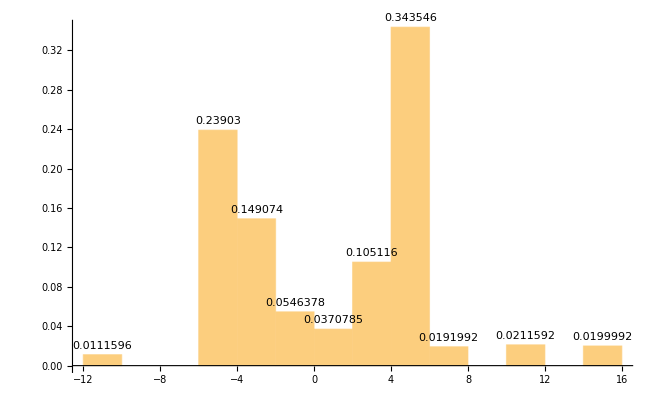

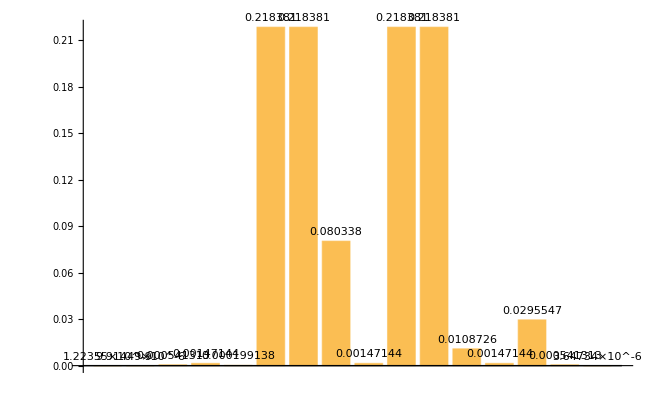

```mathematica
ClearAll["Global`*"];

T=1; (*Set temperature T to 1*)
tsim=50; (*Set simulation duration time tsim to 50*)

h={1,1,1,1}; (*h is a vector[1,1,1,1]*)
J={{0,-3,-2,-1},{-3,0,-1.5,-0.5},{-2,-1.5,0,-2},{-1,-0.5,-2,0}};
(*J is a 4x4 symmetric matrix with 0 on the diagonals and symmetric off-diagonal elements*)

mm={m1[t],m2[t],m3[t],m4[t]};
(*mm is a list of the four functions m1[t],m2[t],m3[t],and m4[t].These are always equal to either-1 or 1. m is the output of a c-bit.*)

xinit={0,0,0,0};
(*xinit is a list of the four initial values of x1,x2,x3,and x4,the auxiliary variables that zigzag like a billiard*)

minit={0,0,0,0};
(*minit is a list of the four initial values of m1,m2,m3,and m4,which is the c-bit output*)

z=h+J.mm;
(*z is a vector with 4 elements,each corresponding to a combination of the h vector and J matrix multiplied by the state vector mm*)

sol=First@NDSolve[{x1'[t]==-m1[t]+Tanh[z[[1]]/T],x2'[t]==-m2[t]+Tanh[z[[2]]/T],x3'[t]==-m3[t]+Tanh[z[[3]]/T],x4'[t]==-m4[t]+Tanh[z[[4]]/T],x1[0]==xinit[[1]],m1[0]==minit[[1]],x2[0]==xinit[[2]],m2[0]==minit[[2]],x3[0]==xinit[[3]],m3[0]==minit[[3]],x4[0]==xinit[[4]],m4[0]==minit[[4]],WhenEvent[x1[t]==1,m1[t]->1],WhenEvent[x1[t]==-1,m1[t]->-1],WhenEvent[x2[t]==1,m2[t]->1],WhenEvent[x2[t]==-1,m2[t]->-1],WhenEvent[x3[t]==1,m3[t]->1],WhenEvent[x3[t]==-1,m3[t]->-1],WhenEvent[x4[t]==1,m4[t]->1],WhenEvent[x4[t]==-1,m4[t]->-1]},{x1,m1,x2,m2,x3,m3,x4,m4},{t,0,tsim},DiscreteVariables->{m1,m2,m3,m4}];

(*The solution sol now contains x1[t],x2[t],x3[t],x4[t],m1[t],m2[t],m3[t],and m4[t] over the time interval[0,tsim].*)

pointsPerTimeStep=500; (*Set the number of points between t=0 and t=1,or t=1 and t=2,etc.*)
time=Range[0.,tsim,1/pointsPerTimeStep];
(*time is a list of equally spaced t values between 0 and tsim*)

m1vals=Map[m1/. sol,time];
m2vals=Map[m2/. sol,time];
m3vals=Map[m3/. sol,time];
m4vals=Map[m4/. sol,time];
(*m1vals,m2vals,m3vals,and m4vals are lists of the values of m1,m2,m3,and m4 corresponding to the t values in time*)

index=2^3*m1vals+2^2*m2vals+2^1*m3vals+2^0*m4vals;
(*index is a list that converts the binary values of m1,m2,m3,m4 into a decimal index*)

Histogram[index,16,"Probability",LabelingFunction->(Placed[#,Above]&)]
(*Plots a histogram of all the values in index.Has 16 bins,one for each possible combination of m1,m2,m3,and m4."Probability" specifies that the heights should be probabilities or fractions,not counts.LabelingFunction puts the labels at the top of each bar.*)

st={st1,st2,st3,st4};
(*The vector,or list st is set to st1,st2,st3,st4.These are new variables that have not already been defined.*)

en=-h.Transpose[st]-0.5*st.J.Transpose[st];
(*en is the energy function derived from h and J.*)

Energy1={en/. {st1->-1,st2->-1,st3->-1,st4->-1},en/. {st1->-1,st2->-1,st3->-1,st4->1},en/. {st1->-1,st2->-1,st3->1,st4->-1},en/. {st1->-1,st2->-1,st3->1,st4->1},en/. {st1->-1,st2->1,st3->-1,st4->-1},en/. {st1->-1,st2->1,st3->-1,st4->1},en/. {st1->-1,st2->1,st3->1,st4->-1},en/. {st1->-1,st2->1,st3->1,st4->1},en/. {st1->1,st2->-1,st3->-1,st4->-1},en/. {st1->1,st2->-1,st3->-1,st4->1},en/. {st1->1,st2->-1,st3->1,st4->-1},en/. {st1->1,st2->-1,st3->1,st4->1},en/. {st1->1,st2->1,st3->-1,st4->-1},en/. {st1->1,st2->1,st3->-1,st4->1},en/. {st1->1,st2->1,st3->1,st4->-1},en/. {st1->1,st2->1,st3->1,st4->1}};
(*Compute the energy for all possible combinations of the states*)

ptemp=Exp[-Energy1/T];
prob=1/Total[ptemp]*ptemp;
BarChart[prob,LabelingFunction->(Placed[#,Above]&)]
(*Plots a bar chart of the probabilities for each state configuration based on the Boltzmann distribution*)
```